```mathematica
X=First[Import["import_data.xlsx"]];
```

```mathematica
s2 = {516224.2474, 152.8577908, 36344.70917, 322.7734214, 180314.4087, 439.7225455, 19.73503143};
```

```mathematica
S=Round[Covariance[X],0.01];
```

XX - центрирование и нормализация данных

```mathematica
XX=Standardize[X];
```

```mathematica
SS=Round[Covariance[XX],0.01]
```

{{1.,0.83,0.84,0.26,-0.38,0.5,0.15},{0.83,1.,0.89,0.24,-0.6,0.42,0.23},{0.84,0.89,1.,0.33,-0.66,0.49,0.27},{0.26,0.24,0.33,1.,-0.11,0.59,-0.18},{-0.38,-0.6,-0.66,-0.11,1.,0.18,-0.22},{0.5,0.42,0.49,0.59,0.18,1.,0.08},{0.15,0.23,0.27,-0.18,-0.22,0.08,1.}}

```mathematica
lambda=Det[S]^(166/2)/Product[i^(166/2),{i,s2}]
```

7.41236550101701×10^-208

```mathematica
ro = 1-(2*7+11)/(6*166)//N
```

0.9749

```mathematica
theta = -2*ro*Log[lambda]
```

929.927

```mathematica
ownLambda = Round[Eigenvalues[SS],0.01]
```

{3.55,1.53,0.94,0.64,0.18,0.12,0.04}

```mathematica
ownVectors=Round[Eigenvectors[SS], 0.01]
```

{{-0.47,-0.49,-0.51,-0.23,0.32,-0.31,-0.15},{0.02,-0.12,-0.09,0.55,0.46,0.55,-0.39},{0.02,-0.06,-0.04,-0.22,0.44,0.38,0.78},{0.45,0.21,0.03,-0.64,0.4,0.04,-0.43},{-0.67,0.19,0.21,-0.36,-0.21,0.51,-0.19},{0.22,-0.81,0.41,-0.17,-0.22,0.19,-0.06},{-0.29,0.03,0.71,0.12,0.49,-0.4,0.}}

```mathematica
Part[ownVectors,7]//MatrixForm
```

(-0.29
0.03
0.71
0.12
0.49
-0.4
0.)

```mathematica
ownVectorsTranspose = Transpose[ownVectors];
```

```mathematica
AllDisp = Total[ownLambda]
```

7.

```mathematica
Tr[SS]
```

7.

Доля дисперсии объясняемой каждой компонентой

```mathematica
For[i=1,i<=7,i++,Print[Part[ownLambda,i]/AllDisp, " ", i]]
```

0.507143 1

0.218571 2

0.134286 3

0.0914286 4

0.0257143 5

0.0171429 6

0.00571429 7

Доля дисперсии совокупностью компонент (двух, трех)

```mathematica
s[1] = Part[ownLambda,1]/AllDisp;
```

```mathematica
s[2]=Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp;
```

```mathematica
s[3]=Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp;
```

```mathematica
s[4]= Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp+Part[ownLambda,4]/AllDisp;
```

```mathematica
s[5]= Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp+Part[ownLambda,4]/AllDisp+Part[ownLambda,5]/AllDisp;
```

```mathematica
s[6]=Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp+Part[ownLambda,4]/AllDisp+Part[ownLambda,5]/AllDisp+Part[ownLambda,6]/AllDisp;
```

```mathematica
s[7]=Part[ownLambda,1]/AllDisp+Part[ownLambda,2]/AllDisp+Part[ownLambda,3]/AllDisp+Part[ownLambda,4]/AllDisp+Part[ownLambda,5]/AllDisp+Part[ownLambda,6]/AllDisp+Part[ownLambda,7]/AllDisp;
```

Отбор главных компонент
1) По доле выделенной дисперсии

```mathematica
i=1;
```

```mathematica
While[s[i]<=0.7, Print[s[i+ 1], " ", i+1]; i++]
```

0.725714 2

2) Критерий  Кайзера

```mathematica
i=1;
```

```mathematica
While[Part[ownLambda, i]*7/Tr[SS]>=1, Print[Part[ownLambda, i]*7/Tr[SS]]; i++]
```

3.55203

1.52618

3) Критерий каменистой осыпи

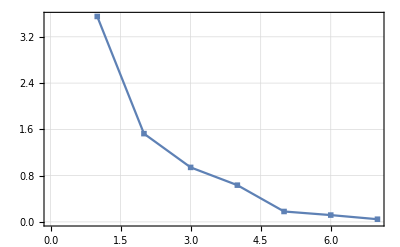

```mathematica
ListPlot[ownLambda, Frame->True,GridLines->Automatic,PlotLegends->"lambda", Joined->True,PlotMarkers->{■, 20}]
```

4)Правило сломанной трости

```mathematica
normOwnLambda = Round[ownLambda/Tr[SS],0.001]
```

{0.507,0.219,0.134,0.091,0.026,0.017,0.006}

```mathematica
listL = {};
```

```mathematica
For[i=1,i<=7,i++, AppendTo[listL,1/7*Sum[1/j,{j,i,7}]]]
```

```mathematica
Round[listL,0.001]//N
```

{0.37,0.228,0.156,0.109,0.073,0.044,0.02}

```mathematica
i=1;
```

```mathematica
While[normOwnLambda[[i]]>=listL[[i]],Print[i];i++]
```

1

Запишем выражение для всех компонент компонент

```mathematica
η1 = XX.Transpose[ownVectors[[1]]];
η2 = XX.Transpose[ownVectors[[2]]];
η3 = XX.Transpose[ownVectors[[3]]];
η4 = XX.Transpose[ownVectors[[4]]];
η5 = XX.Transpose[ownVectors[[5]]];
η6 = XX.Transpose[ownVectors[[6]]];
η7 = XX.Transpose[ownVectors[[7]]];
```

Запишем выражение для главных компонент

```mathematica
Subscript[η, 1] =Subscript[β^(1), 1] Subscript[ξ, 1]+Subscript[β^(1), 2] Subscript[ξ, 2]+Subscript[β^(1), 3] Subscript[ξ, 3]+Subscript[β^(1), 4] Subscript[ξ, 4]+Subscript[β^(1), 5] Subscript[ξ, 5]+Subscript[β^(1), 6] Subscript[ξ, 6]+Subscript[β^(1), 7] Subscript[ξ, 7];
Subscript[η, 2] =Subscript[β^(2), 1] Subscript[ξ, 1]+Subscript[β^(2), 2] Subscript[ξ, 2]+Subscript[β^(2), 3] Subscript[ξ, 3]+Subscript[β^(2), 4] Subscript[ξ, 4]+Subscript[β^(2), 5] Subscript[ξ, 5]+Subscript[β^(2), 6] Subscript[ξ, 6]+Subscript[β^(2), 7] Subscript[ξ, 7];
```

Получим оценки векторов значений главных компонент по всем наблюдениям

```mathematica
η1 = XX.ownVectorsTranspose[[1]]
η2 = XX.ownVectorsTranspose[[2]]
```

{-2.39568,-2.88441,-2.35611,-2.42562,-2.62222,-2.25688,-1.70964,-1.31379,-1.37814,-1.28642,-1.29587,-1.0299,-1.27005,-1.42991,-1.90257,-1.9912,-2.35021,-2.1708,-2.51808,-1.78134,-1.4364,-1.20444,-1.2842,-1.30527,-1.49246,-1.76887,-1.75599,-1.43008,-1.28085,-1.35304,-1.00491,-1.00067,-0.915493,-0.935794,-0.886938,-0.731195,-0.834777,-1.20625,-1.08694,-0.927769,-0.969813,-1.06109,-1.27325,-1.14049,-1.19203,-1.1524,-0.996856,-1.19746,-1.56006,-1.2893,-0.980286,-0.424986,-0.4486,-0.692598,-0.681069,-0.665165,-0.257654,-0.515271,-0.377992,-0.282547,-0.046834,-0.214881,-0.14179,-0.148483,-0.119794,0.225013,-0.107163,0.118415,0.252034,0.54847,0.696727,0.456349,0.454267,0.521614,0.656489,0.76059,0.679591,1.05052,1.40009,1.3415,1.43925,1.22568,0.986794,1.18399,1.15188,0.884256,1.24581,1.22917,1.19701,1.13467,1.09018,0.858324,0.792791,1.32225,1.32082,1.36251,1.18056,1.2935,1.10223,0.891193,0.638432,0.409465,0.294948,-0.060194,-0.134798,-0.264467,-0.235548,0.0907372,0.312754,0.43011,0.462886,0.451071,0.480793,0.740317,0.854962,0.83169,0.797698,0.682807,0.591603,0.489302,0.705358,1.01658,0.847322,0.370301,0.243325,0.317348,0.546774,0.481852,0.369329,0.371175,0.397273,0.387136,0.445725,0.523838,0.562273,0.505079,0.558948,0.506407,0.470413,0.619596,0.605407,0.541381,0.68507,0.686923,0.444847,0.491288,0.526759,0.864094,1.21752,1.08269,1.63552,1.64619,1.4462,1.41675,1.40925,1.56119,1.40641,1.41543,1.23373,1.28087,1.10654,1.28352,1.35976,1.36929,1.629,1.63826}

{2.90592,3.01939,2.08326,2.44141,2.5446,2.26525,2.21184,2.23091,1.66938,1.76952,1.8905,1.16411,0.242196,-0.123055,-0.128096,-0.88715,-0.798574,-0.333041,-0.00354437,-0.266816,-0.350305,-0.468731,-1.37984,-2.13262,-1.56064,-1.49707,-1.63501,-2.36156,-2.80552,-2.10852,-1.8842,-1.59198,-2.01881,-2.18774,-2.09851,-1.41952,-1.35747,-0.980577,-1.66828,-1.77225,-1.05614,-0.926386,-0.201328,0.554939,0.314925,0.174069,0.640403,0.844973,0.650997,0.267686,0.198924,-0.00667581,0.483351,0.76262,0.81069,1.15153,1.50657,0.669757,0.470892,-0.0970836,0.140679,0.12398,-0.0692015,0.0713438,0.216144,0.510784,0.383954,0.301381,0.604597,0.524589,0.247752,0.961234,0.416694,0.220379,0.542916,0.274137,0.426887,0.0705719,-0.0871779,0.44546,0.643786,-0.135585,-0.681506,-0.218093,-0.489568,-0.708031,-0.319637,-0.0163458,0.0345634,0.178483,0.176653,0.0315397,-0.153404,0.141266,0.38101,0.717129,0.365404,0.220908,1.28258,0.69049,0.373859,0.321711,0.139209,-0.123456,0.295614,0.433331,0.463502,0.260112,0.141393,0.176072,0.228065,0.403962,0.48796,0.391201,0.544602,0.472952,0.637438,0.387742,0.372889,0.381237,0.660838,0.478905,0.479419,0.154896,0.114671,0.803145,0.494302,0.531407,0.233547,0.137623,-0.0827851,-0.0235235,0.0428288,0.235292,-0.03499,0.0696195,0.530382,0.872473,0.812152,0.317703,0.47202,0.512733,-0.122045,-0.305883,-0.663451,-1.06407,-0.676841,-0.754888,-1.08433,-0.918078,-0.817846,-1.05518,-1.22501,-1.17468,-0.9938,-0.666481,-0.888224,-0.393554,-0.478605,-0.253394,-0.582568,-1.09052,-1.39924,-1.8903,-1.29115,-1.11426}

```mathematica
B = ownVectors
```

{{-0.47,-0.49,-0.51,-0.23,0.32,-0.31,-0.15},{0.02,-0.12,-0.09,0.55,0.46,0.55,-0.39},{0.02,-0.06,-0.04,-0.22,0.44,0.38,0.78},{0.45,0.21,0.03,-0.64,0.4,0.04,-0.43},{-0.67,0.19,0.21,-0.36,-0.21,0.51,-0.19},{0.22,-0.81,0.41,-0.17,-0.22,0.19,-0.06},{-0.29,0.03,0.71,0.12,0.49,-0.4,0.}}

Определим какие признаки вносят наибольший вклад в каждую главную компоненту

```mathematica
B^2
```

{{0.2209,0.2401,0.2601,0.0529,0.1024,0.0961,0.0225},{0.0004,0.0144,0.0081,0.3025,0.2116,0.3025,0.1521},{0.0004,0.0036,0.0016,0.0484,0.1936,0.1444,0.6084},{0.2025,0.0441,0.0009,0.4096,0.16,0.0016,0.1849},{0.4489,0.0361,0.0441,0.1296,0.0441,0.2601,0.0361},{0.0484,0.6561,0.1681,0.0289,0.0484,0.0361,0.0036},{0.0841,0.0009,0.5041,0.0144,0.2401,0.16,0.}}

```mathematica
maxelement1 =Position[ B[[1]]^2,Max[(B^2)[[1]]]]
maxelement2 = Position[ B[[2]]^2,Max[(B^2)[[2]]]]
maxelement3 = Position[ B[[3]]^2,Max[(B^2)[[3]]]]
maxelement4 = Position[ B[[4]]^2,Max[(B^2)[[4]]]]
maxelement5 = Position[ B[[5]]^2,Max[(B^2)[[5]]]]
maxelement6 = Position[ B[[6]]^2,Max[(B^2)[[6]]]]
maxelement7 = Position[ B[[7]]^2,Max[(B^2)[[7]]]]
```

{{3}}

{{4},{6}}

{{7}}

{{4}}

{{1}}

{{2}}

{{3}}

```mathematica
Total[Transpose[B^2]]
```

{0.995,0.9916,1.0004,1.0036,0.999,0.9896,1.0036}

```mathematica
(B^2)[[1,3]]+(B^2)[[1,1]]+ (B^2)[[1,2]]
```

0.7211

```mathematica
(B^2)[[2,4]]+(B^2)[[2,6]]
```

0.605